Here I want to find the area of a circle in the worst way possible
This approach is motivated by finding the delay distribution in a MCP pore
The sensible thing to do is to prove the approach with a circle then move on


given a unit circle
x=cos(ϕ)
y=sin(ϕ)

displace a circle up by w and find the arc length that remains in the original circle
integrate this arc length in order to find the circle area

```mathematica
xpos[p_]=Cos[p];
ypos[p_]=Sin[p];
wmax:=2*ypos[π/2];
```

```mathematica
intersectionpts=Solve[{xpos[a]==xpos[b], 
ypos[a]==ypos[b]+w},{a,b}]
```

{{a→ConditionalExpression[ArcTan[-1/2 √(4-w^2),w/2]+2 π C[1],C[1]∈ℤ],b→ConditionalExpression[ArcTan[-1/2 √(4-w^2),-w/2]+2 π C[2],C[2]∈ℤ]},{a→ConditionalExpression[ArcTan[(√(4-w^2))/2,w/2]+2 π C[1],C[1]∈ℤ],b→ConditionalExpression[ArcTan[(√(4-w^2))/2,-w/2]+2 π C[2],C[2]∈ℤ]}}

```mathematica
Intersect11=intersectionpts[[2,1,2]]/.C[1]->0
Intersect12=intersectionpts[[1,1,2]]/.C[1]->0
Intersect21=intersectionpts[[2,2,2]]/.C[2]->0
Intersect22=intersectionpts[[1,2,2]]/.C[2]->0
```

ArcTan[(√(4-w^2))/2,w/2]

ArcTan[-1/2 √(4-w^2),w/2]

ArcTan[(√(4-w^2))/2,-w/2]

ArcTan[-1/2 √(4-w^2),-w/2]

```mathematica
ypos[(3 π)/2]
```

-1

## Area Under the region between intersections

The idea that the arc length is the right thing to relate some small segment of depths to the surface area at the detector surface is not strictly correct
instead it is better to think about what the change in 


Find the area between the x axis and the circle arc between intersection points
A=∫y(x)ⅆx 
do a change of var
x=cos(ϕ)
dx/dϕ=-sin(ϕ)
A=∫y(ϕ)(-sin(ϕ)) ⅆϕ

```mathematica
Manipulate[
Module[{wtmp,wtmp2},
wtmp=wfac*wmax;
wtmp2=0.01*wmax;
Show[
ParametricPlot[{xpos[a],ypos[a]},{a,-π,π},PlotLabel->StringForm["``.",wfac],
PlotRange->{{-1.5,1.5},{-1,1}*wmax}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,-π,π}],
ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w->wtmp,Intersect11/.w->wtmp},PlotStyle->{Red}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,Intersect21/.w->wtmp,Intersect22/.w->wtmp},PlotStyle->{Green}]
]],{wfac,10^-6,0.99999}
]
```

π+1/4 (-w √(4-w^2)-(-2+4 w) ArcTan[-√(4-w^2),-w]-(2-4 w) ArcTan[√(4-w^2),-w])+1/4 (-w √(4-w^2)-2 ArcTan[-√(4-w^2),w]+2 ArcTan[√(4-w^2),w])

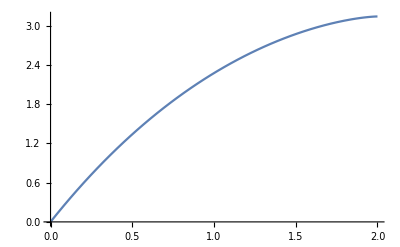

```mathematica
areaArc=π-Integrate[(w+ypos[ϕ] * D[xpos[ϕ],ϕ])  ,{ϕ,Intersect21,Intersect22}]-Integrate[ypos[ϕ] * D[xpos[ϕ],ϕ]  ,{ϕ,Intersect12,Intersect11}]
Plot[areaArc,{w,0,wmax}]
```

```mathematica
dareaArc=FullSimplify[D[areaArc,w],Assumptions->{w∈Reals,w>0}]
```

((-2+w) w)/(√(4-w^2))-ArcTan[-√(4-w^2),-w]+ArcTan[√(4-w^2),-w]

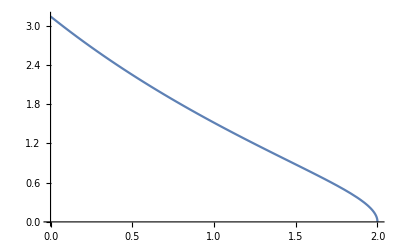

```mathematica
Plot[dareaArc,{w,0,wmax}]
```

```mathematica
Integrate[Abs[dareaArc],{w,0,wmax}]
```

π

```mathematica
N[(ArcTan[-√(4-w^2),-w]+ArcTan[√(4-w^2),-w]+π)/.w->1.5]
```

0.

## Arc length (old)

```mathematica
ArcLenIndef=Integrate[√((D[xpos[ϕ],ϕ])^2+(D[ypos[ϕ],ϕ])^2),ϕ]
ArcLenDefManual=(ArcLenIndef/.ϕ->Intersect1)-(ArcLenIndef/.ϕ->Intersect2)
```

ϕ

-ArcTan[-1/2 √(4-w^2),-w/2]+ArcTan[(√(4-w^2))/2,-w/2]

```mathematica
FullSimplify[(ArcLenDefManual/.w->0)*wmax]
```

-2 π

```mathematica
NIntegrate[ArcLenDefManual,{w,0,wmax},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10]
```

4.

```mathematica
Manipulate[
Module[{wtmp,wtmp2},
wtmp=wfac*wmax;
wtmp2=0.01*wmax;
Show[
ParametricPlot[{xpos[a],ypos[a]},{a,-π,π},PlotLabel->StringForm["``.,``.",wfac,N[Re[ArcLenDefManual/.w->wtmp],2]],
PlotRange->{{-1.5,1.5},{-1,1}*wmax}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,-π,π}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,Intersect1/.w->wtmp,Intersect2/.w->wtmp},PlotStyle->{Red}],
ParametricPlot[{xpos[a],ypos[a]+wtmp+wtmp2},{a,Intersect1/.w->wtmp,Intersect2/.w->wtmp},PlotStyle->{Red}]
]],{wfac,10^-6,0.99999}
]
```

```mathematica
ListPlot[{{xpos[Intersect1],zpos[Intersect1]+d},{xpos[Intersect2],zpos[Intersect2]+d}}/.{α->alphaTemp,d->b},PlotStyle->Red,PlotMarkers->{Automatic, Medium}],
PlotRange->{{-1.1,1.1},zmax[alphaTemp]*{-0.7,0.8}}
```